# Calculation of Statistical-Mechanical Quantities of Lotka-Volterra Hamiltonian

## (#1): Requisite Data:

## (#1.1): “Standard LV Hamiltonian”

### (#1.1.1): Defining the Hamiltonian:

```mathematica
LVHamiltonian[q_,p_]:=δ Exp[p]-γ p + β Exp[q]-α q;
```

### (#1.1.2): Can we easily exponentiate it?

```mathematica
Exp[LVHamiltonian[q,p]]
```

ⅇ^(-q α+ⅇ^q β-p γ+ⅇ^p δ)

## (#2): Microcanonical Ensemble Analysis (“Standard Hamiltonian”):

## (#2.1): Obtaining the Area Enclosed by Phase Space Orbits:

### (#2.1.1): Making a plot for visualizing the orbits:

Using the following article for the values of the parameter: https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example

```mathematica
LVHamiltonian[q,p]==1/.α->2/3/.β->4/3/.γ->1/.δ->1
```

ⅇ^p+(4 ⅇ^q)/3-p-(2 q)/3==1

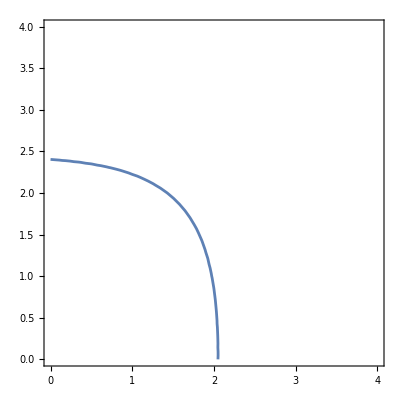

```mathematica
ContourPlot[
ⅇ^p+(4 ⅇ^q)/3-p-(2 q)/3==10,{q,0,4},{p,0,4}
]
```

### (#2.1.2): Trying to Solve

```mathematica
FullSimplify[
Solve[ConstE==LVHamiltonian[q,p],p],
Assumptions-> -∞<q<∞&&α∈Reals&&β∈Reals&&δ∈Reals&&γ∈Reals]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→-(ConstE+q α-ⅇ^q β+γ ProductLog[-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ}}

```mathematica
FullSimplify[
Integrate[
-ProductLog[0,x]+ProductLog[1,x],
{x, a, b}],
Assumptions->a>0&&b>0&&b>a]
```

ⅇ^ProductLog[a]-ⅇ^ProductLog[b]-ⅇ^ProductLog[1,a]+ⅇ^ProductLog[1,b]+a ProductLog[a]-b ProductLog[b]-a ProductLog[1,a]+b ProductLog[1,b]

```mathematica
D
```

## (#3): Canonical Ensemble Analysis:

## (#3.1): Partition Function:

### (#3.1.1): Defining the entire Partition Function:

```mathematica
Z[θ_]:=Exp[-θ LVHamiltonian[q,p]]
```

### (#3.1.2): Defining the Z_p Part:

```mathematica
Zp[θ_]:=Exp[-θ(δ Exp[p]-γ p)]
```

### (#3.1.3): Defining the Z_q Part:

```mathematica
Zq[θ_]:=Exp[-θ(β Exp[q]-α q)]
```

### (#3.1.4): Integrating the Z_p Part:

```mathematica
ZpIntegral=Integrate[Zp[θ],{p,-∞,∞},Assumptions->θ∈Reals&&δ∈Reals&&γ ∈Reals]
```

ConditionalExpression[(δ θ)^(-γ θ) Gamma[γ θ], (γ>0&&δ>0&&θ>0)||(γ<0&&δ<0&&θ<0)]

### (#3.1.5): Integrating the Z_q Part:

```mathematica
ZqIntegral=Integrate[Zq[θ],{q,-∞,∞},Assumptions->θ∈Reals&&α∈Reals&&β ∈Reals]
```

ConditionalExpression[(β θ)^(-α θ) Gamma[α θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.1.6): Cross-checking: Z_p Z_q should equal Z:

```mathematica
ZIntegral=Integrate[Z[θ],{q,-∞,∞},{p,-∞,∞},Assumptions->θ∈Reals&&α∈Reals&&β ∈Reals&&δ∈Reals&&γ ∈Reals]
```

ConditionalExpression[(β θ)^(-α θ) (δ θ)^(-γ θ) Gamma[α θ] Gamma[γ θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

We need to confirm that the result is the same as doing the single integral all at once.

```mathematica
ZpIntegral ZqIntegral - ZIntegral
```

ConditionalExpression[0, ]

### (#3.1.7): Plotting Z(θ) with some test parameters:

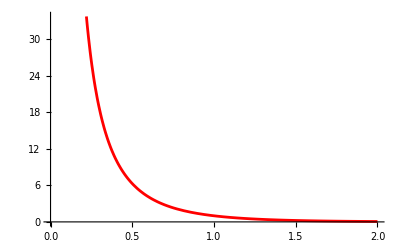

```mathematica
Plot[
ZIntegral/.α->1/.β->1/.γ->1/.δ->1,
{θ,0,2},
PlotStyle->Red
]
```

## (#3.2): Average Energy, ⟨E⟩=-∂/(∂ β)log(Z):

### (#3.2.1): Quantitative calculation using the standard formula:

```mathematica
EnergyAverage=-D[Log[ZIntegral],θ]//FullSimplify
```

ConditionalExpression[α+γ+α Log[β θ]+γ Log[δ θ]-α PolyGamma[0,α θ]-γ PolyGamma[0,γ θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.2.2): Plotting ⟨E⟩(θ ) with some test parameters:

```mathematica
Reals
```

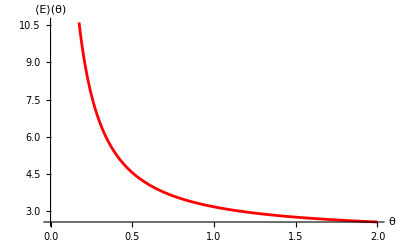

```mathematica
Plot[
EnergyAverage/.α->1/.β->1/.γ->1/.δ->1,
{θ,0,2},
PlotStyle->Red,
AxesLabel->{"θ","⟨E⟩(θ)"}
]
```

## (#3.3): Variance of Average Energy, (ΔE)^2=-(∂⟨E⟩)/(∂ β):

### (#3.3.1): Quantitative calculation using the standard formula:

```mathematica
EnergyVariance=-D[EnergyAverage,θ]//FullSimplify
```

ConditionalExpression[-(α+γ-α^2 θ PolyGamma[1,α θ]-γ^2 θ PolyGamma[1,γ θ])/θ, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.3.2): Plotting (ΔE)^2(θ) with some test parameters:

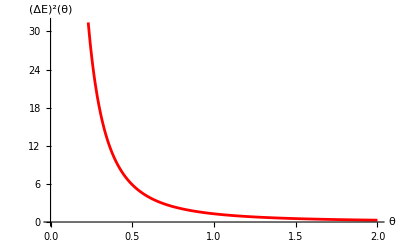

```mathematica
Plot[
EnergyVariance/.α->1/.β->1/.γ->1/.δ->1,
{θ,0,2},
PlotStyle->Red,
AxesLabel->{"θ","(ΔE)^2(θ)"}
]
```

```mathematica
Integrate[x[t]/y[t],t]
```

∫x[t]/y[t]ⅆt

```mathematica
Integrate[1/(u A + (1-u)B)^2,{u,0,1},Assumptions->A∈Reals&&B∈Reals]
```

ConditionalExpression[1/(A B), A≠B&&(A^2≤A B||B^2≤A B)]

```mathematica
Integrate[1/(u 1/A+ (1-u)B)^2,{u,0,1},Assumptions->A∈Reals&&B∈Reals]
```

A/B

```mathematica
Integrate[1/(u 1/A+ (1-u)B)^2,t,Assumptions->A∈Reals&&B∈Reals]
```